## Figure G2 Mathematica File

This code will reproduce Fig G2 of Supplementary Material Section G. Labels were added to the plot in PowerPoint.

### Define Functions

```mathematica
(*This function gives the invasion funtion for type i. It uses the analytical solutions for the 1-consumer-1-resource equilibria for type i and calculates the key quantities from equation 10 *)
InvasionCondition[taui_,tauj_,ai_,aj_,e_,m_,k_,r_,βi_,βj_]:=Module[{Si,Hi,RiI,ωji,ωij,Pj,RjE,invasionCondition},

(*Define the expressions*)
Si=r (ai k (e-m taui)-m (m taui+1))/(ai m (1+(k r ai taui)/(βi+m)));(*Searcher at Equilibrium for i*)
Hi=(r taui (ai (e k-k m taui)-m (1+m taui)))/(ai ((m r taui (1+m taui))/(m+βi)+e-m taui));(*Handler at Equilibrium for i*)
RiI=m (m taui+1) (1+(k r ai taui)/(βi+m))/(ai (e+m taui ((r (m taui+1))/(βi+m)-1))); (*Resource at Equilibrium for i*)
ωji=(βi+m)/(βi+βj+2 m); (*prob j wins contest*)
ωij=(βj+m)/(βi+βj+2 m); (*prob i wins contest*)
Pj=1/(1+((aj Hi)/(βi+βj+2 m))+((ai Si)/(1/tauj+m) (ωij+aj(Hi+RiI)/(βi+βj+2 m))));  (* Cost of interference*)
RjE=(m (m tauj+1))/(aj (e-m tauj));  (*Exploitative Rstar for j*)

(*Calculate the invasion condition*)
invasionCondition=Pj (RiI+ωji Hi)-RjE; (*Note that in contrast to equation 10, we have subtracted RjE from each side to give Subscript[I, j]-Subscript[E, ji]. j invades if Subscript[I, j]-Subscript[E, ji]>0*)
(*Return the result*)
invasionCondition]

(*This function calculates Subscript[β, 0] (centering the plot) *)
OptimalBeta[τ_,e_,m_,a_,k_,r_]:=Re[(m^2 τ (3-r τ)-m (-1+2 e+r τ)+√m √(1+m τ) √(m+4 a e k r τ+m r^2 τ^2-2 m r τ (1+2 a k τ)+m^2 τ (-1+r τ)^2))/(2 (e-m τ))];
```

## Set Parameters

Here, we set the parameters used in the below plots. Parameters are the same as those used in Fig. 3 in the main text.

```mathematica
tau=1; (*handling time (same for both types in Fig. 3)*)
a = .1; (*attack rate (same for both types in Fig. 3)*)
e=.035; (*conversion efficiency*)
m=.015; (*baseline mortality*)
k=250; (*resource capacity*)
r=.26; (*resource renewal rate*)

(* Parameter that scales plots *)
SCALE = 10 ;
```

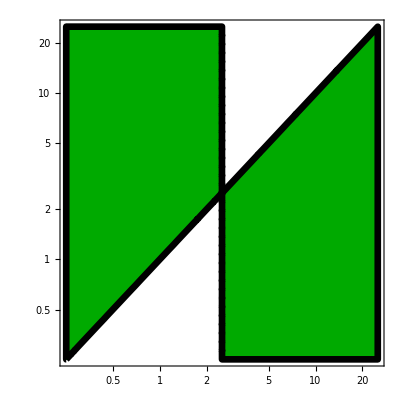

```mathematica
FigCoexA0=RegionPlot[{InvasionCondition[tau,tau,a,a,e,m,k,r,β1,β2]>0},{β1,OptimalBeta[tau,e,m,a,k,r]/SCALE,OptimalBeta[tau,e,m,a,k,r]*SCALE},{β2,OptimalBeta[tau,e,m,a,k,r]/SCALE,OptimalBeta[tau,e,m,a,k,r]*SCALE},GridLines->None,PlotLegends->None,PlotStyle->{Directive[Red,Opacity[.4]],Directive[Darker[Green],Opacity[1]]},BoundaryStyle-> Directive[Black,Thickness[.012]],
FrameTicksStyle->{{Directive[Black,FontSize->15],Automatic},{Directive[FontOpacity->1,FontSize->15],Automatic}},FrameTicks->{{Round[OptimalBeta[tau,e,m,a,k,r],.1]/SCALE,Round[OptimalBeta[tau,e,m,a,k,r],.1],Round[OptimalBeta[tau,e,m,a,k,r],.1]*SCALE},{Round[OptimalBeta[tau,e,m,a,k,r],.1]/SCALE,Round[OptimalBeta[tau,e,m,a,k,r],.1],Round[OptimalBeta[tau,e,m,a,k,r],.1]*SCALE}},FrameStyle->Directive[Black,AbsoluteThickness[2.5]],PlotLegends->{None,None},ScalingFunctions->{"Log","Log"},PlotLegends->None]
```